```mathematica
Clear[μ,λ,s,k]
```

```mathematica
QueueProperties[QueueingProcess[μ,λ,s],"MeanSystemTime"]
```

1/λ+(s λ (μ/λ)^s Gamma[s])/((s λ-μ) (s λ (μ/λ)^s Gamma[s]-ⅇ^(μ/λ) (-s λ+μ) s! Gamma[s,μ/λ]))

```mathematica
Clear[λ,μ,s,ρ,LQ,WQ,P0]
```

```mathematica
μ=(5.6)/30;
λ=1/11.1;
s=3;
ρ=λ/μ;
LQ=1/(μ-λ)
WQ=(LQ*λ)/μ
P0=ρ^0(1-ρ)
```

10.3545

4.99733

0.517375

```mathematica
LQ=ρ^(s+1)/(Factorial[(s-1)]*(s-ρ)^2)(*ρ^2/(1-ρ)*)*P0
```

4.41794×10^-9

```mathematica
5/30
```

1/6

```mathematica
(3*22.08+6*.5)/9
```

7.69333

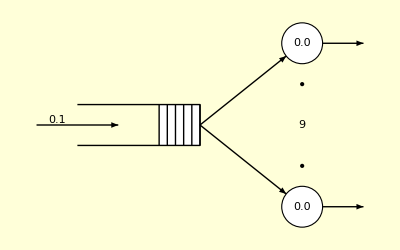
-Graphics- | 
Basic Properties | 
QueueNotation | M/M/9
ArrivalRate | 0.186667
ServiceRate | 0.0900901
UtilizationFactor | 0.230222
Throughput | 0.186667
ServiceChannels | 9
SystemCapacity | ∞
InitialState | 0
Performance Measures | 
MeanSystemSize | 2.07209
MeanSystemTime | 11.1005
MeanQueueSize | 0.000094907
MeanQueueTime | 0.00050843

```mathematica
QueueProperties[QueueingProcess[(5.6/30),1/11.1,9]]
```

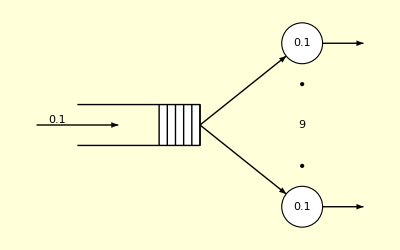
-Graphics- | 
Basic Properties | 
QueueNotation | M/M/9
ArrivalRate | 0.186667
ServiceRate | 0.129983
UtilizationFactor | 0.159565
Throughput | 0.186667
ServiceChannels | 9
SystemCapacity | ∞
InitialState | 0
Performance Measures | 
MeanSystemSize | 1.43609
MeanSystemTime | 7.69335
MeanQueueSize | 3.84693×10^-6
MeanQueueTime | 0.0000206085

```mathematica
QueueProperties[QueueingProcess[(5.6/30),1/7.6933333333333325,9]]
```

## Graphics

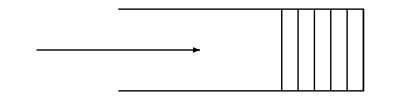

```mathematica
Graphics[{{{GrayLevel[1], Rectangle[{3, -1/2}]}, 
     {{GrayLevel[0], Line[{{3, -1/2}, {3, 1/2}}]}, 
      {GrayLevel[0], Line[{{16/5, -1/2}, {16/5, 1/2}}]}, 
      {GrayLevel[0], Line[{{17/5, -1/2}, {17/5, 1/2}}]}, 
      {GrayLevel[0], Line[{{18/5, -1/2}, {18/5, 1/2}}]}, 
      {GrayLevel[0], Line[{{19/5, -1/2}, {19/5, 1/2}}]}, 
      {GrayLevel[0], Line[{{4, -1/2}, {4, 1/2}}]}}, 
     {GrayLevel[0], Line[{{1, -1/2}, {4, -1/2}, {4, 1/2}, {1, 1/2}}]}}, 
    {GrayLevel[0], Arrow[{{0, 0}, {2, 0}}]}}]
```

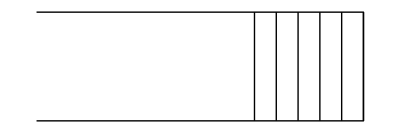

```mathematica
Graphics[{{{GrayLevel[1],Rectangle[{3,-1/2}]},{{GrayLevel[0],Line[{{3,-1/2},{3,1/2}}]},{GrayLevel[0],Line[{{16/5,-1/2},{16/5,1/2}}]},{GrayLevel[0],Line[{{17/5,-1/2},{17/5,1/2}}]},{GrayLevel[0],Line[{{18/5,-1/2},{18/5,1/2}}]},{GrayLevel[0],Line[{{19/5,-1/2},{19/5,1/2}}]},{GrayLevel[0],Line[{{4,-1/2},{4,1/2}}]}},{GrayLevel[0],Line[{{1,-1/2},{4,-1/2},{4,1/2},{1,1/2}}]}}}]
```

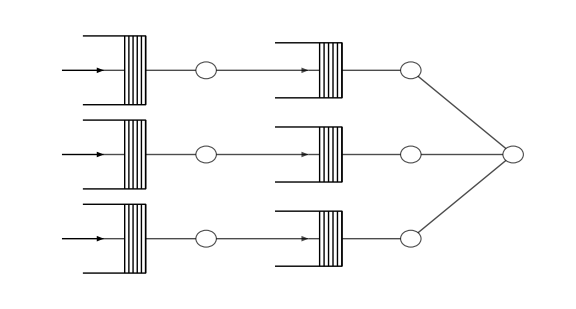

```mathematica
Graph[{1->"node",2->"node1",3->"node2",4->7,5->8,6->9,"node"->4,"node1"->5,"node2"->6,7->10,8->10,9->10},VertexShape->{1->-Graphics-,2->-Graphics-,3->-Graphics-,4->-Graphics-,5->-Graphics-,6->-Graphics-},VertexSize->{1->1,2->1,3->1,4->.8,5->.8,6->.8,7->0.2,8->0.2,9->0.2,10->0.2,"node"->0.2,"node1"->0.2,"node2"->0.2},GraphLayout->{"LayeredDigraphEmbedding","Orientation"->Left},EdgeStyle->Black,VertexStyle->White,EdgeShapeFunction->GraphElementData["FilledArrow","ArrowSize"->0.015],ImageSize->Large]
```

```mathematica
(∑_(i=0)^(s-1) ρ^i/(i!)+ρ^s/(s!)((s*μ)/(s*μ-λ)))^-1
```

0.616744

```mathematica
Table[Subscript[x, i],{i,1,3}]
```

{x_1,x_2,x_3}

```mathematica
Table[Subscript[t, i]->Subscript[x, i] 3.6/Subscript[vmax, i]/.{Subscript[x, i]->2,Subscript[vmax, 1]->40,Subscript[vmax, 2]->25,Subscript[vmax, 3]->40},{i,1,3}]
```

{t_1→0.18,t_2→0.288,t_3→0.18}

```mathematica
Total[Table[Subscript[x, i] 3.6/Subscript[vmax, i]/.{Subscript[x, i]->2,Subscript[vmax, 1]->40,Subscript[vmax, 2]->25,Subscript[vmax, 3]->40},{i,1,3}]]
```

0.648

```mathematica
Table[Subscript[t, i]->Subscript[x, i] 3.6/Subscript[vmax, i]/.{Subscript[x, i]->2,Subscript[vmax, i]->25},{i,1,3}]
```

{t_1→0.288,t_2→0.288,t_3→0.288}

```mathematica
Total[Table[Subscript[x, i] 3.6/Subscript[vmax, i]/.{Subscript[x, i]->2,Subscript[vmax, i]->25},{i,1,3}]]
```

0.864

## Useless Shit

```mathematica
γ=Table[5.6/30,{i,9}]
```

{0.186667,0.186667,0.186667,0.186667,0.186667,0.186667,0.186667,0.186667,0.186667}

```mathematica
μ=Table[1/11.1,{i,9}]
```

{0.0900901,0.0900901,0.0900901,0.0900901,0.0900901,0.0900901,0.0900901,0.0900901,0.0900901}

```mathematica
r=Table[{1,0,0,0,0,0,0,0,0},{i,9}]

c=Table[1,{i,9}];
```

{{1,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0}}